```mathematica
(*The boson kernell*)
```

```mathematica
m=0.01;
```

```mathematica
points =1000;
domain = {0, 20};
```

```mathematica
f0[x_]:=1/(1+E^(x))
B[x_]:=x
```

```mathematica
NonLimitIntegrandDiag[w_,wp_]:=B[w+wp](Coth[(w+wp)/2]-Tanh[wp/2])+B[w-wp](Coth[(w-wp)/2]+Tanh[wp/2])
```

```mathematica
LimitIntegrandDiag[w_]=Limit[B[w+wp](Coth[(w+wp)/2]-Tanh[wp/2])+B[w-wp](Coth[(w-wp)/2]+Tanh[wp/2]),wp-> w]
```

2+2 w Csch[w]

```mathematica
IntegrandDiag[w_,wp_]:=Table[If[w==wp[[i]],LimitIntegrandDiag[w],NonLimitIntegrandDiag[w,wp[[i]]]],{i,points}]/(2Pi)
```

```mathematica
NonDiagIntegrandFerm[w_,wp_]:=B[w+wp](Coth[(w+wp)/2]-Tanh[w/2])-B[w-wp](Coth[(w-wp)/2]-Tanh[w/2])
DiagIntegrandFerm[w_]=Limit[B[w+wp](Coth[(w+wp)/2]-Tanh[w/2])-B[w-wp](Coth[(w-wp)/2]-Tanh[w/2]),wp-> w]
IntegrandFerm[w_,wp_]:=If[w==wp,DiagIntegrandFerm[w],NonDiagIntegrandFerm[w,wp]]/(2 Pi)
```

-2+2 w Csch[w]

```mathematica
IntB[x_,w_,wp_]:=1/(2Pi x)B[x](Tanh[(w+x)/2]+Tanh[(w-x)/2]-2 Tanh[w/2])(Tanh[(wp+x)/2]+Tanh[(wp-x)/2])
```

```mathematica
IntegrandB[w_,wp_]:=NIntegrate[IntB[x,w,wp],{x,0,1000},Exclusions->{0}]
```

```mathematica
(*Computing the calculation basis*)
```

```mathematica
{nodes,weights}=Most[NIntegrate`GaussRuleData[points,MachinePrecision]];
```

```mathematica
midgrid=Rescale[nodes,{0,1},domain];
weightsSK=weights *domain[[2]];
```

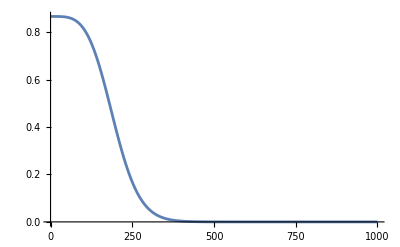

```mathematica
f1=(-D[f0[x],{x,1}]/Sqrt[Integrate[Evaluate[D[f0[y],{y,1}]]^2,{y,0,Infinity}]])/.{x->midgrid};
ListLinePlot[f1, PlotRange->All]
NumIntegrate[x_,y_]:=Total[weightsSK*x*y]
WIntegrate[x_,y_]:=Total[weightsSK*(f1^2)*x*y]
WIntegrate3[x_,A_,y_]:=Total[x*f1*weightsSK*(A.(f1 * y *weightsSK))]
```

```mathematica
ClearAll[TestFN,TestFNUnnorm]
```

```mathematica
X=midgrid;
```

```mathematica
TestFNUnnorm[n_Integer]:=TestFNUnnorm[n]=FullSimplify[(X^2 * TestFN[n-1]-Evaluate[Sum[TestFN[i]*WIntegrate[TestFN[i],X^2*TestFN[n-1]],{i,n-1}]])]
TestFN[n_Integer]:=TestFN[n]=TestFNUnnorm[n]/Sqrt[WIntegrate[TestFNUnnorm[n],TestFNUnnorm[n]]]
TestFN[1]:=X/Sqrt[WIntegrate[X,X]]
```

```mathematica
Nb=6;
Basis=Table[TestFN[n],{n,Nb}];
```

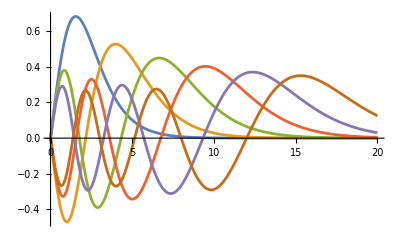

```mathematica
ListLinePlot[Table[Transpose[{midgrid,Basis[[i]]*f1}],{i,Nb}]]
```

```mathematica
Table[WIntegrate[Basis[[i]],Basis[[j]]],{i,Nb},{j,Nb}]
```

{{1.,1.80478×10^-16,-2.03074×10^-16,2.16824×10^-16,-2.14631×10^-16,1.92861×10^-16},{1.80478×10^-16,1.,2.90922×10^-17,-3.01805×10^-17,3.41133×10^-17,-2.10036×10^-17},{-2.03074×10^-16,2.90922×10^-17,1.,-2.49177×10^-16,1.43076×10^-16,-9.98721×10^-17},{2.16824×10^-16,-3.01805×10^-17,-2.49177×10^-16,1.,-3.27223×10^-16,2.23315×10^-16},{-2.14631×10^-16,3.41133×10^-17,1.43076×10^-16,-3.27223×10^-16,1.,5.44704×10^-16},{1.92861×10^-16,-2.10036×10^-17,-9.98721×10^-17,2.23315×10^-16,5.44704×10^-16,1.}}

```mathematica
(*Computing the matrix elements of operators*)
```

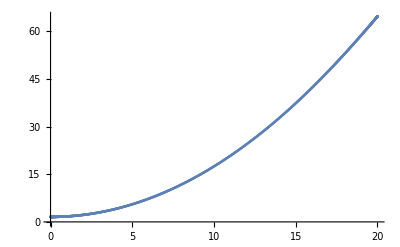

```mathematica
g=Table [NumIntegrate[IntegrandDiag[X[[i]],X],ConstantArray[1, points]],{i,points}];
ListPlot[Transpose[{midgrid,g}]]
```

```mathematica
gdelf=Table[WIntegrate[Basis[[i]],g*Basis[[j]]],{i,Nb},{j,Nb}]
```

{{2.30856,0.738208,-3.72405×10^-7,-3.7799×10^-7,-3.17468×10^-7,-2.04556×10^-7},{0.738208,4.29875,2.09859,-0.0000106678,-0.0000140946,-0.0000131465},{-3.72405×10^-7,2.09859,7.81589,4.25115,-0.000206657,-0.000268041},{-3.7799×10^-7,-0.0000106678,4.25115,12.9139,7.18967,-0.00244888},{-3.17468×10^-7,-0.0000140946,-0.000206657,7.18967,19.5406,10.813},{-2.04556×10^-7,-0.0000131465,-0.000268041,-0.00244888,10.813,27.0254}}

```mathematica
{vals, vecs}=Eigensystem[gdelf];
```

```mathematica
vals
```

{35.5706,18.6193,9.8422,5.17688,2.85066,1.8434}

```mathematica
(*Operator is completely positive, makes sense*)
```

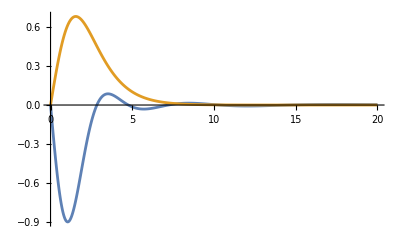

```mathematica
eigvecsg=vecs.Basis;
ListLinePlot[{Table[Transpose[{midgrid,eigvecsg[[i]]*f1}],{i,Nb}][[6]],Table[Transpose[{midgrid,Basis[[i]]*f1}],{i,Nb}][[1]]},PlotRange->All]
```

```mathematica
KerIg=Table[IntegrandFerm[X[[i]],X[[j]]],{i,points},{j,points}];
```

```mathematica
NonDiagF=Table[WIntegrate3[Basis[[i]],KerIg,Basis[[j]]],{i,Nb},{j,Nb}]
```

{{-0.769518,-2.31899,-4.70067,-7.32014,-9.57601,-10.3005},{-0.246068,-1.14774,-3.13177,-5.87349,-8.47869,-9.57716},{9.01178×10^-7,-0.209773,-1.1602,-3.20101,-5.72704,-7.19731},{6.77337×10^-7,0.0000649405,-0.200283,-1.13544,-2.98428,-4.62099},{4.51612×10^-7,0.0000435254,0.00145521,-0.176518,-0.964309,-2.19104},{2.39915×10^-7,0.0000233563,0.000790301,0.0128055,-0.0801872,-0.507723}}

```mathematica
ColIntEq = gdelf+NonDiagF;
```

```mathematica
{vals,vecseq}=Eigensystem[ColIntEq];
Min[Re[vals]]
```

1.9345

```mathematica
vals
```

{32.1808,18.8636,7.9173,5.38752,1.9345+0.146203 ⅈ,1.9345-0.146203 ⅈ}

```mathematica
(*Interestingly, the most slowly decaying mode scillates - blue curve*)
```

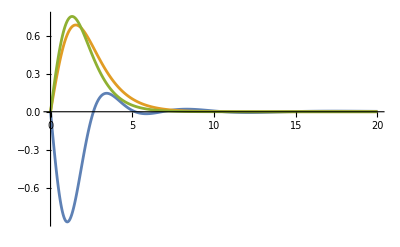

```mathematica
eigvecseq=vecseq.Basis;
ListLinePlot[{Table[Transpose[{midgrid,Re[eigvecseq[[i]]*f1]}],{i,Nb}][[6]],Table[Transpose[{midgrid,Basis[[i]]*f1}],{i,Nb}][[1]],Transpose[{midgrid,2.25Tanh[X/2]*f1}]},PlotRange->All]
```

```mathematica
(*Incorporating the boson*)
```

```mathematica
ClearAll[x]
```

```mathematica
Monitor[KerIb=Table[IntegrandB[X[[i]],X[[j]]],{i,points},{j,points}],ProgressIndicator[i,{0,points}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {21.5545}. NIntegrate obtained -3.10968×10^-11 and 3.17188×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {21.5545}. NIntegrate obtained -3.0427×10^-11 and 3.16361×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {21.5545}. NIntegrate obtained -2.97734×10^-11 and 3.15549×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Collision_Integral_FL.mx"}],KerIb]
```

C:\Users\Serhii Kryhin\Dropbox (Harvard University)\non-linear transport\Paper backups\PRL_v4\Git data\Collision_Integral_FL.mx

```mathematica
KerIb=Import[FileNameJoin[{NotebookDirectory[],"Collision_Integral_FL.mx"}]]
```

```mathematica
Ib=Table[WIntegrate3[Basis[[i]],KerIb,Basis[[j]]],{i,Nb},{j,Nb}]
gdelf+NonDiagF
ColIntEq = gdelf+NonDiagF+ Ib
```

{{-1.53904,-4.63798,-9.40134,-14.6403,-19.152,-20.6011},{-0.492137,-2.29549,-6.26353,-11.747,-16.9574,-19.1543},{1.8025×10^-6,-0.419547,-2.32039,-6.40202,-11.4541,-14.3946},{1.3546×10^-6,0.00012988,-0.400566,-2.27089,-5.96857,-9.24198},{9.03181×10^-7,0.0000870505,0.00291041,-0.353036,-1.92862,-4.38209},{4.79934×10^-7,0.0000467133,0.0015806,0.0256111,-0.160374,-1.01545}}

{{1.53904,-1.58078,-4.70067,-7.32014,-9.57601,-10.3005},{0.49214,3.151,-1.03317,-5.8735,-8.4787,-9.57718},{5.28773×10^-7,1.88882,6.65569,1.05014,-5.72724,-7.19758},{2.99347×10^-7,0.0000542727,4.05086,11.7785,4.20539,-4.62344},{1.34145×10^-7,0.0000294308,0.00124855,7.01315,18.5763,8.62199},{3.53599×10^-8,0.0000102098,0.00052226,0.0103566,10.7329,26.5177}}

{{3.23358×10^-6,-6.21876,-14.102,-21.9604,-28.728,-30.9016},{3.01664×10^-6,0.855515,-7.29671,-17.6205,-25.4361,-28.7315},{2.33127×10^-6,1.46927,4.3353,-5.35189,-17.1813,-21.5922},{1.65395×10^-6,0.000184153,3.6503,9.50759,-1.76318,-13.8654},{1.03733×10^-6,0.000116481,0.00415896,6.66011,16.6476,4.23991},{5.15294×10^-7,0.000056923,0.00210286,0.0359677,10.5725,25.5022}}

```mathematica
{vals,vecsb}=Eigensystem[ColIntEq];
Min[Re[vals]];
```

```mathematica
vals
```

{22.8581+4.26799 ⅈ,22.8581-4.26799 ⅈ,4.99696+2.99582 ⅈ,4.99696-2.99582 ⅈ,1.13821,0.0000380611}

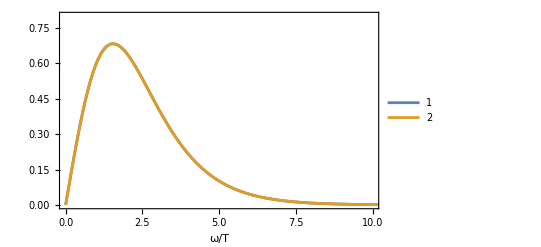

```mathematica
eigvecsb=vecsb.Basis;
ListLinePlot[{Table[Transpose[{midgrid,-Re[eigvecsb[[i]]*f1]}],{i,Nb}][[6]],Table[Transpose[{midgrid,Basis[[i]]*f1}],{i,Nb}][[1]]},PlotRange->{{0,10},{0,0.8}},Frame->True,Axes->False,PlotLegends->Automatic,FrameLabel->{"ω/T"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14}]
```

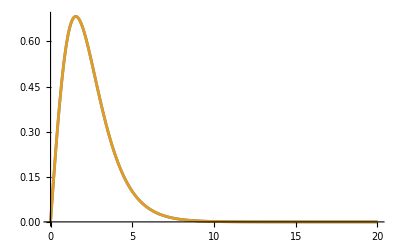

```mathematica
ListLinePlot[{Table[Transpose[{midgrid,-Re[eigvecsb[[i]]*f1]}],{i,Nb}][[6]],Table[Transpose[{midgrid,Basis[[i]]*f1}],{i,Nb}][[1]]},PlotRange->All]
```

```mathematica
Matr=Table[Conjugate[vecsb[[i]]].vecsb[[j]],{i,Nb},{j,Nb}];
Matr//MatrixForm
```

(1.+0. ⅈ | 0.590809-0.0693385 ⅈ | 0.4118+0.0279163 ⅈ | 0.0949793+0.170301 ⅈ | -0.203499-0.12687 ⅈ | -0.235414-0.187879 ⅈ
0.590809+0.0693385 ⅈ | 1.+0. ⅈ | 0.0949793-0.170301 ⅈ | 0.4118-0.0279163 ⅈ | -0.203499+0.12687 ⅈ | -0.235414+0.187879 ⅈ
0.4118-0.0279163 ⅈ | 0.0949793+0.170301 ⅈ | 1.+0. ⅈ | 0.206357+0.172864 ⅈ | -0.559938+0.105418 ⅈ | -0.668403+2.77607×10^-6 ⅈ
0.0949793-0.170301 ⅈ | 0.4118+0.0279163 ⅈ | 0.206357-0.172864 ⅈ | 1.+0. ⅈ | -0.559938-0.105418 ⅈ | -0.668403-2.77607×10^-6 ⅈ
-0.203499+0.12687 ⅈ | -0.203499-0.12687 ⅈ | -0.559938-0.105418 ⅈ | -0.559938+0.105418 ⅈ | 1.+0. ⅈ | 0.958168+0. ⅈ
-0.235414+0.187879 ⅈ | -0.235414-0.187879 ⅈ | -0.668403-2.77607×10^-6 ⅈ | -0.668403+2.77607×10^-6 ⅈ | 0.958168+0. ⅈ | 1.+0. ⅈ)

```mathematica
Inverse[Matr]//MatrixForm
```

(8.1175-8.88178×10^-15 ⅈ | -7.304+0.813464 ⅈ | -2.29033+7.16499 ⅈ | 2.24357+6.74824 ⅈ | -0.164691-18.0645 ⅈ | 0.470888+29.6973 ⅈ
-7.304-0.813464 ⅈ | 8.1175-6.21725×10^-15 ⅈ | 2.24357-6.74824 ⅈ | -2.29033-7.16499 ⅈ | -0.164691+18.0645 ⅈ | 0.470888-29.6973 ⅈ
-2.29033-7.16499 ⅈ | 2.24357+6.74824 ⅈ | 11.6123-2.04281×10^-14 ⅈ | 8.29552-3.47903 ⅈ | -24.103+2.20488 ⅈ | 39.0042-5.38799 ⅈ
2.24357-6.74824 ⅈ | -2.29033+7.16499 ⅈ | 8.29552+3.47903 ⅈ | 11.6123-1.59872×10^-14 ⅈ | -24.103-2.20488 ⅈ | 39.0042+5.38799 ⅈ
-0.164691+18.0645 ⅈ | -0.164691-18.0645 ⅈ | -24.103-2.20488 ⅈ | -24.103+2.20488 ⅈ | 77.4405-1.73617×10^-13 ⅈ | -113.288+2.83881×10^-13 ⅈ
0.470888-29.6973 ⅈ | 0.470888+29.6973 ⅈ | 39.0042+5.38799 ⅈ | 39.0042-5.38799 ⅈ | -113.288+2.36536×10^-13 ⅈ | 173.07-3.894×10^-13 ⅈ)

```mathematica
ebasis=vecsb.Basis;
```

```mathematica
fbasis=Conjugate[Inverse[Matr]].vecsb.Basis;
```

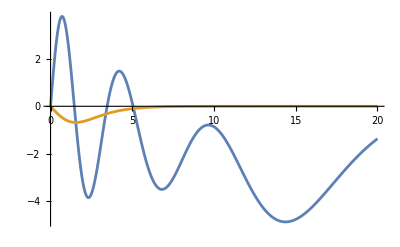

```mathematica
ListLinePlot[{Table[Transpose[{midgrid,Re[fbasis[[i]]*f1]}],{i,Nb}][[6]],Table[Transpose[{midgrid,Re[ebasis[[i]]*f1]}],{i,Nb}][[6]]},PlotRange->All]
```

```mathematica
WIntegrate[Conjugate[fbasis[[6]]],ebasis[[6]]]
```

1.+3.62844×10^-15 ⅈ

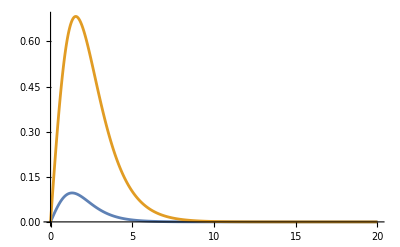

```mathematica
f2=Evaluate[D[f0[x],{x,2}]]/.{x->X};
ListLinePlot[{Transpose[{midgrid,f2}],Table[Transpose[{midgrid,Basis[[i]]*f1}],{i,Nb}][[1]]},PlotRange->All]
```

```mathematica
Total[-weightsSK*f1*fbasis[[6]]*f2]*N[6/Sqrt[Pi^2-6]]*Pi
```

0.499993-6.44502×10^-15 ⅈ

```mathematica
D[x^2D[f0[x],x],x]//FullSimplify
```

(x (-2+x Tanh[x/2]))/(2 (1+Cosh[x]))

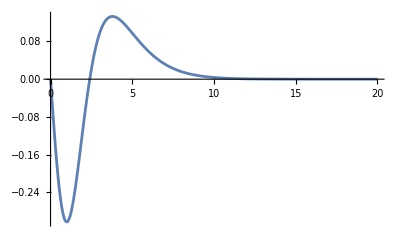

2.83008+1.33614×10^-14 ⅈ

```mathematica
f3=Evaluate[D[x^2D[f0[x],x],x]]/.{x->X};
ListLinePlot[Transpose[{midgrid,f3}],PlotRange->All]
Total[-weightsSK*f1*fbasis[[6]]*f3]*N[6/Sqrt[Pi^2-6]]
```

```mathematica
Total[-weightsSK*f1*fbasis[[6]]*f3]*N[6/Sqrt[Pi^2-6]]/(Pi^2)*Pi
```

0.900843+4.25305×10^-15 ⅈ

```mathematica
N[6/Sqrt[Pi^2-6]]
```

3.05013

```mathematica
basisf6=x D[f0[x],x]/Sqrt[Integrate[(x D[f0[y],y]/.{y->x})^2,{x,0,Infinity}]]
```

-(6 ⅇ^x x)/((1+ⅇ^x)^2 √(-6+π^2))

```mathematica
Integrate[basisf6^2,{x,0,Infinity}]
```

1

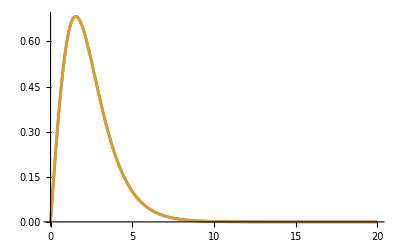

```mathematica
ListLinePlot[{Transpose[{midgrid,-basisf6/.{x->X}}],Table[Transpose[{midgrid,-Re[ebasis[[i]]*f1]}],{i,Nb}][[6]]},PlotRange->All]
```

```mathematica
D[f0[w/T],{T,1}]
```

(ⅇ^(w/T) w)/((1+ⅇ^(w/T))^2 T^2)

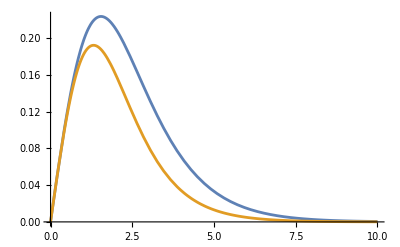

```mathematica
Plot[{-x (Evaluate[D[f0[y],y]]/.{y->x}),2(Evaluate[D[f0[y],{y,2}]]/.{y->x})},{x,0,10}]
```

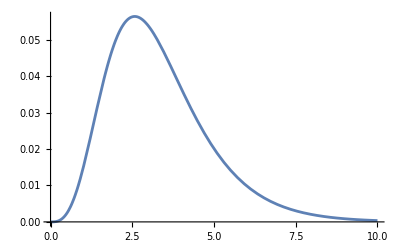

```mathematica
Plot[-x (Evaluate[D[f0[y],y]]/.{y->x})-2(Evaluate[D[f0[y],{y,2}]]/.{y->x}),{x,0,10}]
```